```mathematica
ClearAll["Global`*"]
```

#### Ge76

```mathematica
enBMGe={-0.90000,-0.80000,-0.70000,-0.60000,-0.50000,-0.40000,-0.30000,-0.20000,-0.10000,0.00000,0.10000,0.20000,0.30000,0.40000,0.50000,0.60000,0.70000,0.80000,0.90000,1.00000,1.10000,1.20000,1.30000,1.40000,1.50000,1.60000,1.70000,1.80000,1.90000,2.00000,2.10000,2.20000,2.30000,2.40000,2.50000,2.60000,2.70000,2.80000,2.90000,3.00000,3.10000,3.20000,3.30000,3.40000,3.50000,3.60000,3.70000,3.80000,3.90000,4.00000,4.10000,4.20000,4.30000,4.40000,4.50000,4.60000,4.70000,4.80000,4.90000,5.00000,5.10000,5.20000,5.30000,5.40000,5.50000,5.60000,5.70000,5.80000,5.90000,6.00000,6.10000,6.20000,6.30000,6.40000,6.50000,6.60000,6.70000,6.80000,6.90000,7.00000,7.10000,7.20000,7.30000,7.40000,7.50000,7.60000,7.70000,7.80000,7.90000,8.00000,8.10000,8.20000,8.30000,8.40000,8.50000,8.60000,8.70000,8.80000,8.90000,9.00000,9.10000,9.20000,9.30000,9.40000,9.50000,9.60000,9.70000,9.80000,9.90000,10.00000,10.10000,10.20000,10.30000,10.40000,10.50000,10.60000,10.70000,10.80000,10.90000,11.00000,11.10000,11.20000,11.30000,11.40000,11.50000,11.60000,11.70000,11.80000,11.90000,12.00000,12.10000,12.20000,12.30000,12.40000,12.50000,12.60000,12.70000,12.80000,12.90000,13.00000,13.10000,13.20000,13.30000,13.40000,13.50000,13.60000,13.70000,13.80000,13.90000,14.00000,14.10000,14.20000,14.30000,14.40000,14.50000,14.60000,14.70000,14.80000,14.90000,15.00000,15.10000,15.20000,15.30000,15.40000,15.50000,15.60000,15.70000,15.80000,15.90000,16.00000,16.10000,16.20000,16.30000,16.40000,16.50000,16.60000,16.70000,16.80000,16.90000,17.00000,17.10000,17.20000,17.30000,17.40000,17.50000,17.60000,17.70000,17.80000,17.90000,18.00000,18.10000,18.20000,18.30000,18.40000,18.50000,18.60000,18.70000,18.80000,18.90000,19.00000,19.10000,19.20000,19.30000,19.40000,19.50000,19.60000,19.70000,19.80000,19.90000,20.00000,20.10000,20.20000,20.30000,20.40000,20.50000,20.60000,20.70000,20.80000,20.90000,21.00000};
strBMGe={0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00001,0.00003,0.00007,0.00017,0.00039,0.00085,0.00172,0.00331,0.00604,0.01046,0.01717,0.02677,0.03972,0.05619,0.07604,0.09889,0.12432,0.15229,0.18346,0.21949,0.26288,0.31653,0.38274,0.46195,0.55169,0.64585,0.73509,0.80819,0.85436,0.86582,0.83982,0.77944,0.69282,0.59117,0.48617,0.38771,0.30242,0.23335,0.18062,0.14251,0.11673,0.10136,0.09543,0.09889,0.11229,0.13606,0.16985,0.21209,0.25992,0.30980,0.35833,0.40323,0.44387,0.48097,0.51571,0.54828,0.57688,0.59745,0.60459,0.59326,0.56070,0.50768,0.43864,0.36061,0.28154,0.20848,0.14629,0.09722,0.06118,0.03647,0.02063,0.01118,0.00603,0.00367,0.00322,0.00429,0.00695,0.01152,0.01852,0.02847,0.04170,0.05818,0.07738,0.09823,0.11930,0.13911,0.15652,0.17101,0.18285,0.19281,0.20180,0.21031,0.21808,0.22402,0.22660,0.22444,0.21704,0.20526,0.19154,0.17956,0.17374,0.17860,0.19848,0.23800,0.30354,0.40571,0.56217,0.79962,1.15313,1.66097,2.35417,3.24207,4.29758,5.44808,6.57756,7.54313,8.20362,8.45287,8.24699,7.61599,6.65591,5.50409,4.30653,3.18797,2.23273,1.47939,0.92738,0.54998,0.30858,0.16379,0.08225,0.03908,0.01756,0.00747,0.00300,0.00114,0.00041,0.00014,0.00005,0.00001,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000};
enBPGe={-0.90000,-0.80000,-0.70000,-0.60000,-0.50000,-0.40000,-0.30000,-0.20000,-0.10000,0.00000,0.10000,0.20000,0.30000,0.40000,0.50000,0.60000,0.70000,0.80000,0.90000,1.00000,1.10000,1.20000,1.30000,1.40000,1.50000,1.60000,1.70000,1.80000,1.90000,2.00000,2.10000,2.20000,2.30000,2.40000,2.50000,2.60000,2.70000,2.80000,2.90000,3.00000,3.10000,3.20000,3.30000,3.40000,3.50000,3.60000,3.70000,3.80000,3.90000,4.00000,4.10000,4.20000,4.30000,4.40000,4.50000,4.60000,4.70000,4.80000,4.90000,5.00000,5.10000,5.20000,5.30000,5.40000,5.50000,5.60000,5.70000,5.80000,5.90000,6.00000,6.10000,6.20000,6.30000,6.40000,6.50000,6.60000,6.70000,6.80000,6.90000,7.00000,7.10000,7.20000,7.30000,7.40000,7.50000,7.60000,7.70000,7.80000,7.90000,8.00000,8.10000,8.20000,8.30000,8.40000,8.50000,8.60000,8.70000,8.80000,8.90000,9.00000,9.10000,9.20000,9.30000,9.40000,9.50000,9.60000,9.70000,9.80000,9.90000,10.00000,10.10000,10.20000,10.30000,10.40000,10.50000,10.60000,10.70000,10.80000,10.90000,11.00000,11.10000,11.20000,11.30000,11.40000,11.50000,11.60000,11.70000,11.80000,11.90000,12.00000,12.10000,12.20000,12.30000,12.40000,12.50000,12.60000,12.70000,12.80000,12.90000,13.00000,13.10000,13.20000,13.30000,13.40000,13.50000,13.60000,13.70000,13.80000,13.90000,14.00000,14.10000,14.20000,14.30000,14.40000,14.50000,14.60000,14.70000,14.80000,14.90000,15.00000,15.10000,15.20000,15.30000,15.40000,15.50000,15.60000,15.70000,15.80000,15.90000,16.00000,16.10000,16.20000,16.30000,16.40000,16.50000,16.60000,16.70000,16.80000,16.90000,17.00000,17.10000,17.20000,17.30000,17.40000,17.50000,17.60000,17.70000,17.80000,17.90000,18.00000,18.10000,18.20000,18.30000,18.40000,18.50000,18.60000,18.70000,18.80000,18.90000,19.00000,19.10000,19.20000,19.30000,19.40000,19.50000,19.60000,19.70000,19.80000,19.90000,20.00000,20.10000,20.20000,20.30000,20.40000,20.50000,20.60000,20.70000,20.80000,20.90000,21.00000};
strBPGe={0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00001,0.00002,0.00003,0.00006,0.00009,0.00014,0.00021,0.00029,0.00039,0.00048,0.00057,0.00065,0.00069,0.00071,0.00070,0.00067,0.00063,0.00059,0.00057,0.00057,0.00061,0.00067,0.00074,0.00081,0.00087,0.00091,0.00092,0.00089,0.00084,0.00077,0.00071,0.00065,0.00062,0.00063,0.00069,0.00081,0.00097,0.00119,0.00142,0.00166,0.00187,0.00202,0.00209,0.00207,0.00198,0.00182,0.00163,0.00146,0.00133,0.00128,0.00134,0.00150,0.00177,0.00215,0.00265,0.00327,0.00407,0.00510,0.00640,0.00802,0.00992,0.01198,0.01402,0.01576,0.01695,0.01737,0.01691,0.01562,0.01368,0.01135,0.00891,0.00662,0.00466,0.00311,0.00196,0.00118,0.00068,0.00039,0.00024,0.00017,0.00017,0.00019,0.00024,0.00031,0.00039,0.00050,0.00063,0.00078,0.00096,0.00115,0.00134,0.00152,0.00168,0.00181,0.00191,0.00198,0.00204,0.00210,0.00215,0.00218,0.00218,0.00214,0.00205,0.00192,0.00177,0.00163,0.00154,0.00153,0.00164,0.00191,0.00237,0.00310,0.00421,0.00589,0.00838,0.01195,0.01681,0.02304,0.03045,0.03853,0.04647,0.05325,0.05789,0.05964,0.05817,0.05372,0.04694,0.03882,0.03037,0.02248,0.01575,0.01043,0.00654,0.00388,0.00218,0.00116,0.00058,0.00028,0.00012,0.00005,0.00002,0.00001,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000};
```

#### Se76

```mathematica
enBPSe={-0.90000,-0.80000,-0.70000,-0.60000,-0.50000,-0.40000,-0.30000,-0.20000,-0.10000,0.00000,0.10000,0.20000,0.30000,0.40000,0.50000,0.60000,0.70000,0.80000,0.90000,1.00000,1.10000,1.20000,1.30000,1.40000,1.50000,1.60000,1.70000,1.80000,1.90000,2.00000,2.10000,2.20000,2.30000,2.40000,2.50000,2.60000,2.70000,2.80000,2.90000,3.00000,3.10000,3.20000,3.30000,3.40000,3.50000,3.60000,3.70000,3.80000,3.90000,4.00000,4.10000,4.20000,4.30000,4.40000,4.50000,4.60000,4.70000,4.80000,4.90000,5.00000,5.10000,5.20000,5.30000,5.40000,5.50000,5.60000,5.70000,5.80000,5.90000,6.00000,6.10000,6.20000,6.30000,6.40000,6.50000,6.60000,6.70000,6.80000,6.90000,7.00000,7.10000,7.20000,7.30000,7.40000,7.50000,7.60000,7.70000,7.80000,7.90000,8.00000,8.10000,8.20000,8.30000,8.40000,8.50000,8.60000,8.70000,8.80000,8.90000,9.00000,9.10000,9.20000,9.30000,9.40000,9.50000,9.60000,9.70000,9.80000,9.90000,10.00000,10.10000,10.20000,10.30000,10.40000,10.50000,10.60000,10.70000,10.80000,10.90000,11.00000,11.10000,11.20000,11.30000,11.40000,11.50000,11.60000,11.70000,11.80000,11.90000,12.00000,12.10000,12.20000,12.30000,12.40000,12.50000,12.60000,12.70000,12.80000,12.90000,13.00000,13.10000,13.20000,13.30000,13.40000,13.50000,13.60000,13.70000,13.80000,13.90000,14.00000,14.10000,14.20000,14.30000,14.40000,14.50000,14.60000,14.70000,14.80000,14.90000,15.00000,15.10000,15.20000,15.30000,15.40000,15.50000,15.60000,15.70000,15.80000,15.90000,16.00000,16.10000,16.20000,16.30000,16.40000,16.50000,16.60000,16.70000,16.80000,16.90000,17.00000,17.10000,17.20000,17.30000,17.40000,17.50000,17.60000,17.70000,17.80000,17.90000,18.00000,18.10000,18.20000,18.30000,18.40000,18.50000,18.60000,18.70000,18.80000,18.90000,19.00000,19.10000,19.20000,19.30000,19.40000,19.50000,19.60000,19.70000,19.80000,19.90000,20.00000,20.10000,20.20000,20.30000,20.40000,20.50000,20.60000,20.70000,20.80000,20.90000,21.00000};
strBPSe={0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00001,0.00001,0.00001,0.00002,0.00003,0.00003,0.00004,0.00004,0.00005,0.00005,0.00005,0.00004,0.00004,0.00004,0.00004,0.00004,0.00004,0.00005,0.00005,0.00006,0.00007,0.00007,0.00007,0.00007,0.00006,0.00006,0.00005,0.00004,0.00003,0.00003,0.00003,0.00003,0.00003,0.00003,0.00004,0.00005,0.00007,0.00008,0.00009,0.00011,0.00012,0.00012,0.00012,0.00012,0.00011,0.00010,0.00008,0.00007,0.00007,0.00007,0.00008,0.00010,0.00014,0.00021,0.00030,0.00042,0.00056,0.00071,0.00087,0.00101,0.00113,0.00119,0.00119,0.00113,0.00102,0.00088,0.00071,0.00055,0.00040,0.00027,0.00018,0.00011,0.00007,0.00004,0.00002,0.00002,0.00002,0.00002,0.00003,0.00004,0.00005,0.00006,0.00008,0.00009,0.00010,0.00010,0.00010,0.00010,0.00009,0.00008,0.00008,0.00008,0.00008,0.00008,0.00008,0.00009,0.00010,0.00012,0.00014,0.00016,0.00018,0.00020,0.00021,0.00022,0.00023,0.00024,0.00025,0.00028,0.00034,0.00046,0.00066,0.00095,0.00133,0.00180,0.00232,0.00285,0.00331,0.00364,0.00379,0.00373,0.00348,0.00307,0.00256,0.00202,0.00151,0.00107,0.00071,0.00045,0.00027,0.00015,0.00008,0.00004,0.00002,0.00001,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000,0.00000};
```

## Figure 1

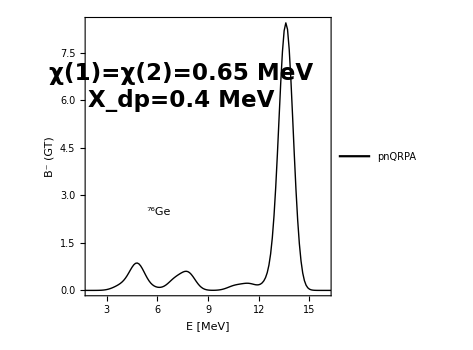

```mathematica
tableFig1=Table[{enBMGe[[i]],strBMGe[[i]]},{i,1,Length[strBMGe]}];
fig1=ListPlot[tableFig1,Joined->True,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{2,16},Full},FrameLabel->{"E [MeV]","B^- (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.65 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.39,0.8}]],Inset[Style["X_dp=0.4 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.39,0.7}]],Inset[Framed[Style[Row[{Superscript["","76"],"Ge"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.3}]]},ImageSize->350];
Show[fig1]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_2/new_figs/fig1_set2.pdf",Show[fig1],ImageResolution->1200];
```

## Figure 2

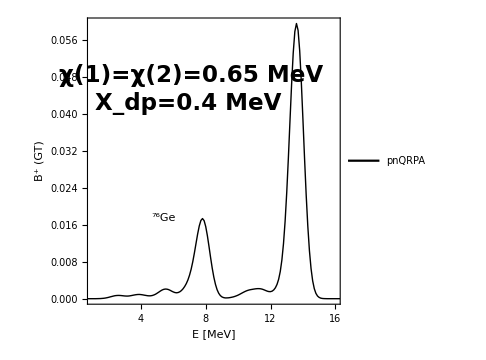

```mathematica
tableFig2=Table[{enBPGe[[i]],strBPGe[[i]]},{i,1,Length[strBPGe]}];
(*ListPlot[tableFig2,Ticks->{Automatic,{#,ScientificForm@#}&/@{0,0.000006,0.000012}},PlotRange->All]*)
fig2=ListPlot[tableFig2,Joined->True,ImageSize->Medium,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{1,16},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{23,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.65 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.41,0.8}]],Inset[Style["X_dp=0.4 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.7}]],Inset[Framed[Style[Row[{Superscript["","76"],"Ge"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.3,0.3}]]},ImageSize->350];
Show[fig2]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_2/new_figs/fig2_set2.pdf",Show[fig2],ImageResolution->1200];
```

## Figure 3

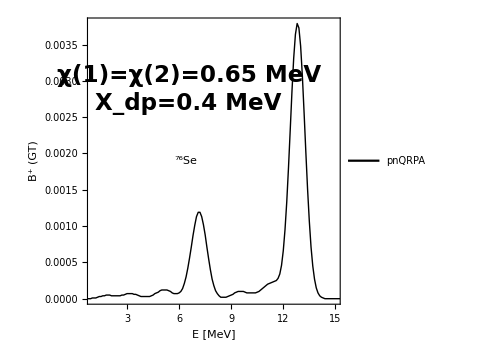

```mathematica
tableFig3=Table[{enBPSe[[i]],strBPSe[[i]]},{i,1,Length[strBPSe]}];
fig3=ListPlot[tableFig3,Joined->True,ImageSize->Medium,AspectRatio->1,Frame->True,Axes->False,FrameStyle->Directive[Black,Thick],PlotStyle->{Thick,Black},PlotRange->{{1,15},Full},FrameLabel->{"E [MeV]","B^+ (GT)"},LabelStyle->{20,Bold,Black,FontFamily->"Times"},PlotLegends->Placed[{"pnQRPA"},{0.35,0.9}],Epilog->{Inset[Style["χ(1)=χ(2)=0.65 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.8}]],Inset[Style["X_dp=0.4 MeV",23,Bold,Black,FontFamily->"Times"],Scaled[{0.4,0.7}]],Inset[Framed[Style[Row[{Superscript["","76"],"Se"}],23,Bold,Black,FontFamily->"Times"]],Scaled[{0.39,0.5}]]},ImageSize->350];
Show[fig3]
Export["/Users/basavyr/Documents/Work/mathematica-useful-algorithms/Physics/Double-Beta-July-2022/pnQRPA_beta_transitions/exp_data_2/new_figs/fig3_set2.pdf",Show[fig3],ImageResolution->1200];
```